{{0.458602,0.511319},{2.,3.}}

{0.472824,0.527176}

{{0.472824,2.},{0.527176,3.}}

2.52718

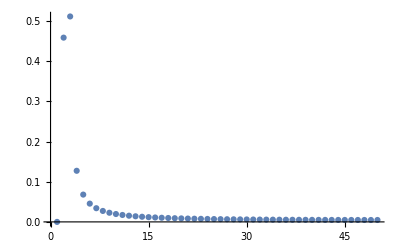

```mathematica
(*Ensure frequency extraction is accurate for straightforward sines*)
DataLength=10.;
SamplingRate=0.01;
XVals=Range[0,DataLength,SamplingRate];
TryGetFreq[truefreq_,offset_]:=(
data=Sin[truefreq*XVals]+Exp[offset-XVals];


Return[]
)

FindPeakIndex[idata_]:=(
data=idata-Mean@idata;
PowerSpec=Abs[Fourier[Normalize@data]];
PowerPeaks=FindPeaks[Take[PowerSpec,Round[0.5Length@idata]]];
peaks=TakeLargestBy[PowerPeaks,Last,1];
Return[peaks⟦1,1⟧];
);

PeakIndexToFreq[index_]:=(2^-0.5*index-2^-0.5)*0.89;
transformedpq=(Take@@{#,0.5Length@#}&)@(Abs@Fourier@Normalize@(Data-Mean@Data));
Peaks=Transpose@N@Select[(First@#)>0.3&]@MapIndexed[({#1,First@#2})&,transformedpq]
Peaks[[1]]=(First@Peaks)/(Total@First@Peaks)
Peaks=Transpose@Peaks
(Function[{a1,a2},a1*a2]@@#&)/@Peaks//Total
ListPlot[transformedpq,PlotRange->All]
(*
FindPeakIndex@Data;
PeakIndexToFreq@FindPeakIndex@Data;
trpq2=10.
outfreqp2=TryGetFreq[5,2.];
Plot[{Sin[5x]+Exp[2-x],Sin[outfreqp2 x]+Exp[2-x]},{x,1,30}]
ListPlot[OutFreqs]
*)
```

```mathematica
PeakIndexToFreq[index_,data_]:=2π*SamplingRate*index/Length[data];
FindPeakIndex[data_,epsilon_]:=
(Function[{a1,a2},a1*a2]@@#&)/@Function[pks,Transpose@{(First@pks)/(Total@First@pks),Last@pks}]@Transpose@N@Select[(First@#)>epsilon&]@MapIndexed[({#1,First@#2})&,Function[sp,Take@@{sp,0.5Length@sp}]@(Abs@Fourier@Normalize@(#-Mean@#))&@data]//Total;

Solve[PeakIndexToFreq@@{FindPeakIndex[Data,0.3],Data}*x==4.,x]
{4.,3.96}
{5.,4.17}
{6.,4.48}
```

{{x→0.629774}}

{4.,3.96}

{5.,4.17}

{6.,4.48}

```mathematica
(*Attempt 3*)
f=Abs@Fourier@Data;
pos=(Position@@{f,Max@f})⟦1,1⟧;
fr = Abs@Fourier[Data Exp[2 Pi I (pos - 2) N@Range[0, DataLength - 1]/DataLength], FourierParameters->{0,2/DataLength}];
frpos = Position[fr, Max[fr]][[1,1]];
DERIFREQ=N[SamplingRate*(pos - 2 + 2 (frpos - 1)/DataLength)/DataLength*2π]
FREQPAIR=Prepend[FREQPAIR,{TRUEFREQ,DERIFREQ}]
```

20.8602

{{21.,20.8602},{20.,19.9805},{19.,18.7239},{18.,17.8442},{17.,16.9646},{16.,15.708},{15.,14.7027},{14.,13.9487},{13.,12.5664},{12.,11.6867},{11.,10.9327},{10.,9.55044},{9.,8.41947},{8.,7.91681},{7.,6.53451},{6.,5.02655},{5.,4.77522},{4.,3.39292},{3.,0.},{2.,0.}}

{{21.,1.0067},{20.,1.00097},{19.,1.01475},{18.,1.00873},{17.,1.00209},{16.,1.01859},{15.,1.02022},{14.,1.00368},{13.,1.03451},{12.,1.02681},{11.,1.00615},{10.,1.04707},{9.,1.06895},{8.,1.01051},{7.,1.07124},{6.,1.19366},{5.,1.04707},{4.,1.17893}}

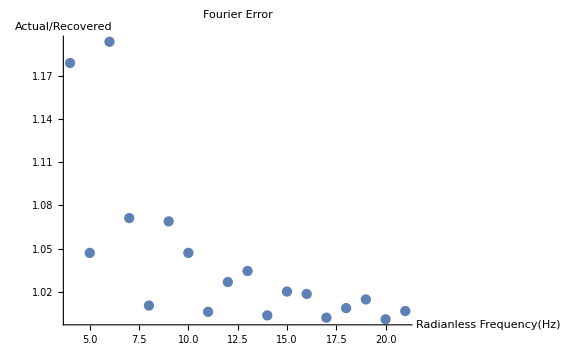

```mathematica
solvedrules=((Solve[First@#==k*Last@#,k]&)/@Select[FREQPAIR,Last@#≠0&]);
FREKPAIK=(k/.solvedrules);
FREKPAIK=Delete[2]/@Join[Select[FREQPAIR,Last@#≠0&],FREKPAIK,2]
ListPlot[FREKPAIK,PlotLabel->"Fourier Error",AxesLabel->{"Radianless Frequency(Hz)","Actual/Recovered"},
ImageSize->Large]
```

```mathematica
(*Minimized and packaged*)
FindMax[list_]:=Position[list,Max@list][[1,1]];
RecoverFrequency[data_,len_,rate_]:=N[(#-2+2(FindMax@Abs@Fourier[data*Exp[2I π(#-2)N@(Range@len-1)/len],FourierParameters->{0,2/len}]-1)/len)*2π*rate/len]&@FindMax@Abs@Fourier@data;
RecoverFrequency[Data,DataLength,SamplingRate]
```

20.8602